## Initialization

```mathematica
SetDirectory[NotebookDirectory[]]
<<MaTeX`
```

/Users/samiyrjanheikki/Documents/FYS/FYSS9470 Erikoistyö

```mathematica
f={#1,Around[#2,#3]}&;
g={#1,#2}&;
h={#1,Around[#2,Scaled[#3]]}&;
```

```mathematica
style={BaseStyle->{FontFamily->"Latin Modern Roman"},Frame->True,FrameStyle->Black};
```

```mathematica
PlotGrid=ResourceFunction["PlotGrid"]
```

```mathematica
colors=ColorData[97,"ColorList"]
```

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.363898, 0.618501, 0.782349],RGBColor[1, 0.75, 0],RGBColor[0.647624, 0.37816, 0.614037],RGBColor[0.571589, 0.586483, 0.],RGBColor[0.915, 0.3325, 0.2125],RGBColor[0.40082222609352647, 0.5220066643438841, 0.85],RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142],RGBColor[0.736782672705901, 0.358, 0.5030266573755369],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]}

```mathematica
HistogramMean[list_]:=Transpose[{list[[1,All,1]],MeanAround/@Transpose[list[[All,All,2]]]}]
```

```mathematica
RelativeError[x_?NumericQ]:=x
RelativeError[around_]:=around["Uncertainty"]/around["Value"]/;Head[around]==Around
```

```mathematica
pTbins={1.0,1.5,2.0,2.5,3.0,3.5,4.0,4.5,5.0,5.5,6.0,6.5,7.0,8.0,9.0,10.0,12.0,15.0};
pTbinCenters=BlockMap[Mean,pTbins,2,1];
pTbinMatrix=BlockMap[Identity,pTbins,2,1];
```

```mathematica
HistogramIntervalize[{h1_,h2_}]:=Transpose[{h1[[All,1]],Interval/@Transpose[{h1[[All,2]],h2[[All,2]]}]}]
```

```mathematica
Conditional[expr_,cond_]:=If[cond,expr,None]
```

```mathematica
Plateau[{a_,b_},h_:1]:=Function[x,Piecewise[{{h,a<x<b},{0,True}}]]
```

```mathematica
AroundValue[expr_]:=expr["Value"]/;Head[expr]==Around
AroundValue[expr_]:=expr
```

```mathematica
StepHistogram[data_,bins_,opts:OptionsPattern[]]:=Plot[data.Through[BlockMap[Plateau[#]&,bins,2,1][x]],{x,Min[bins],Max[bins]},opts]
```

## pT cross section

### PHENIX data

#### Data

```mathematica
hepData=Import["HEP_phenix/Table1.csv"];
pT1=hepData[[All,1]];
σ1raw=hepData[[All,4]];
staterr=Interpreter["Percent"][#]&/@hepData[[All,5]];
syserr=Interpreter["Percent"][#]&/@hepData[[All,7]];
normerr=Interpreter["Percent"][#]&/@hepData[[All,9]];
hepError=√(staterr^2+syserr^2+normerr^2)//UnitConvert;
σ1=Around[#1,Scaled[#2]]&@@@Transpose[{σ1raw,hepError}];
hep=Transpose[{pT1,σ1}];

pythiaData=Import["Pythia/Data/pp/pT/Bias subdivision/1e6/data.csv"];
{pT2,σ2}=Transpose[{#1,Around[#2,#3]}&@@@pythiaData];
pythia=Transpose[{pT2,σ2}];
```

#### Cross section

```mathematica
ConstructStepHistogramData[data_,bins_]:=Module[{matrix,col1,col2},
matrix=BlockMap[Identity,bins,2,1];
col1=matrix[[All,1]];
col2=matrix[[All,2]];
Transpose[{Transpose[{col1,data}],Transpose[{col2,data}]}]
]
```

```mathematica
pTPlot[pythia_,phenix_,bins_,{s1_,s2_},opts__:OptionsPattern[]]:=ListPlot[Join[ConstructStepHistogramData[
AroundValue/@pythia[[All,2]],bins],
{Transpose[{BlockMap[Mean,bins,2,1],phenix[[All,2]]}]}
],opts,PlotStyle->ConstantArray[s1,Length[pythia[[All,2]]]]~Join~ConstantArray[s2,Length[pythia[[All,2]]]],
Joined->ConstantArray[True,Length[pythia[[All,2]]]]~Join~ConstantArray[False,Length[pythia[[All,2]]]]
]
```

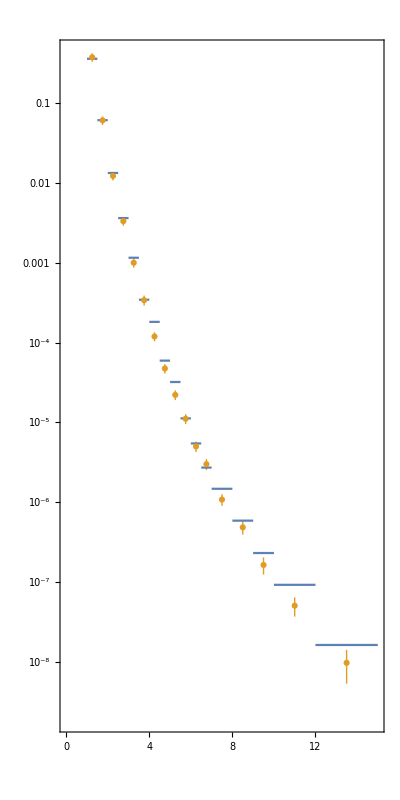

```mathematica
pTdata=pTPlot[pythia,hep,pTbins,colors[[1;;2]],
Evaluate@style,
PlotRange->{{0,15},All},
AspectRatio->2,
ScalingFunctions->"Log",
PlotLegends->{
Placed[
LineLegend[{colors[[1]]},{MaTeX["\\text{Pythia}"]}],
Above
],
Placed[
PointLegend[{colors[[2]]},{MaTeX["\\text{PHENIX}"]},Joined->False],
Above]
}
]
```

#### Error plot

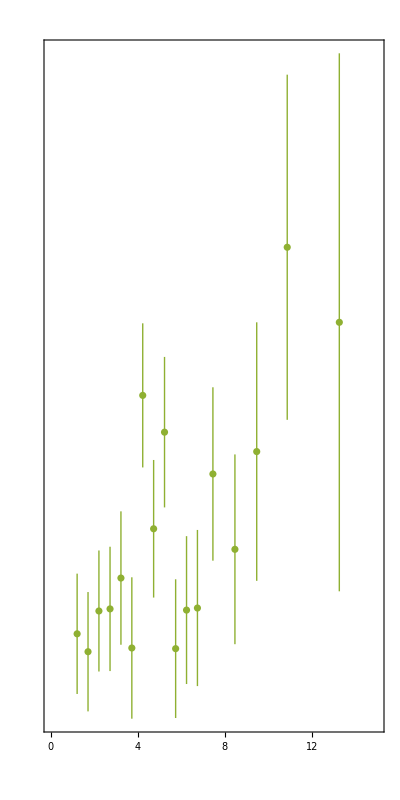

```mathematica
pTerror=ListPlot[
Transpose[{pT1,Abs[σ1-(AroundValue/@σ2)]/σ1}],
IntervalMarkers->"Fences",
Evaluate@style,AspectRatio->2,
PlotStyle->colors[[3]],
PlotLegends->Placed[
PointLegend[{colors[[3]]},{MaTeX["\\text{relative error}"]}],
Above],
FrameTicks->{{None,All},{Automatic,None}},
PlotRange->{{0,15},Automatic}
]
```

#### Combined

```mathematica
pTplot=PlotGrid[{{pTdata,pTerror}},
FrameLabel->MaTeX/@
{"p_T \\ [\\mathrm{GeV}]","\\mathrm{d}\\sigma/\\mathrm{d}p"}]
```

-Graphics-

#### Export

```mathematica
Export["Thesis/Graphics/pTplot.pdf",pTplot]
```

Thesis/Graphics/pTplot.pdf

### Biasing and subdivision of phase space

#### No bias or subdivision

```mathematica
pTNoneData=Import["Pythia/Data/pp/pT/No bias no subdivision/1e5/data.csv"];
{pTNone,σNone}=Transpose[{#1,Around[#2,#3]}&@@@pTNoneData];
pTcsNone=Transpose[{pTNone,σNone}];
```

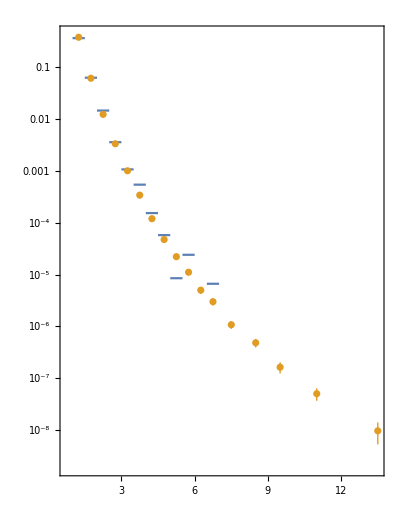

```mathematica
pTPlot1=pTPlot[pTcsNone,hep,pTbins,colors[[1;;2]],
Evaluate@style,
PlotRange->All,
AspectRatio->1.3,
ScalingFunctions->"Log",
PlotLabel->MaTeX["\\text{No bias or subdivision}"]
]
```

#### Bias, no subdivision

```mathematica
pTBiasData=Import["Pythia/Data/pp/pT/Bias no subdivision/1e5/data.csv"];
{pTBias,σBias}=Transpose[{#1,Around[#2,#3]}&@@@pTBiasData];
pTcsBias=Transpose[{pTBias,σBias}];
```

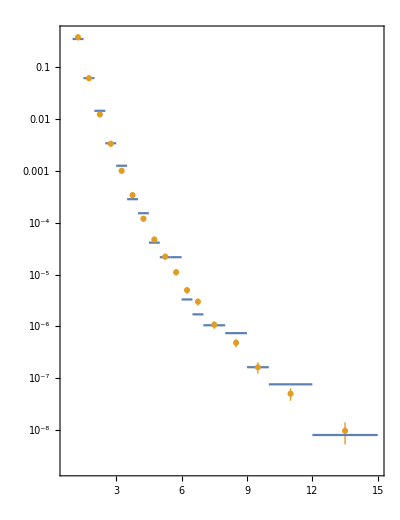

```mathematica
pTPlot2=pTPlot[pTcsBias,hep,pTbins,colors[[1;;2]],
Evaluate@style,
PlotRange->All,
AspectRatio->1.3,
ScalingFunctions->"Log",
PlotLabel->MaTeX["\\text{Bias, no subdivision}"]
]
```

#### No bias, subdivision

```mathematica
pTSubdivisionData=Import["Pythia/Data/pp/pT/No bias subdivision/1e5/data.csv"];
{pTSubdivision,σSubdivision}=Transpose[{#1,Around[#2,#3]}&@@@pTSubdivisionData];
pTcsSubdivision=Transpose[{pTSubdivision,σSubdivision}];
```

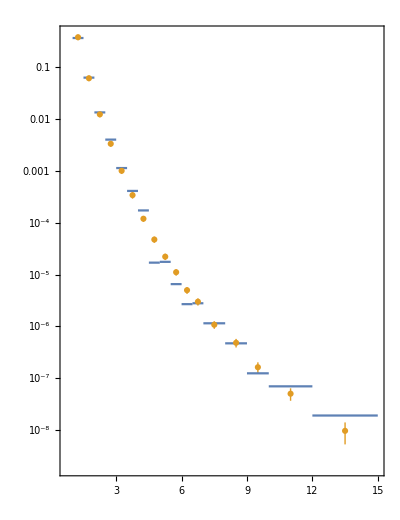

```mathematica
pTPlot4=pTPlot[pTcsSubdivision,hep,pTbins,colors[[1;;2]],
Evaluate@style,
PlotRange->All,
AspectRatio->1.3,
ScalingFunctions->"Log",
PlotLabel->MaTeX["\\text{No bias, subdivision}"]
]
```

#### Bias and subdivision

```mathematica
pTBiasSubdivisionData=Import["Pythia/Data/pp/pT/Bias subdivision/1e5/data.csv"];
{pTBiasSubdivision,σBiasSubdivision}=Transpose[{#1,Around[#2,#3]}&@@@pTBiasSubdivisionData];
pTcsBiasSubdivision=Transpose[{pTBiasSubdivision,σBiasSubdivision}];
```

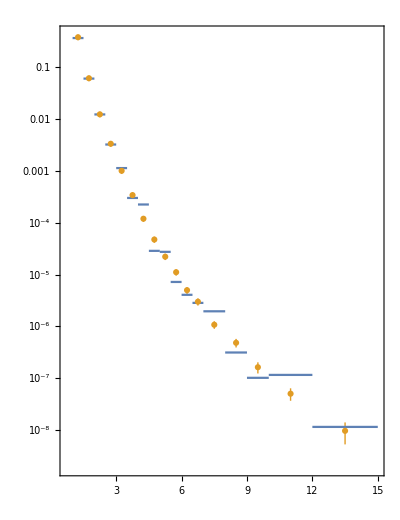

```mathematica
pTPlot3=pTPlot[pTcsBiasSubdivision,hep,pTbins,colors[[1;;2]],
Evaluate@style,
PlotRange->All,
AspectRatio->1.3,
ScalingFunctions->"Log",
PlotLabel->MaTeX["\\text{Bias and subdivision}"],
PlotLegends->{
Placed[
LineLegend[{colors[[1]]},{MaTeX["\\text{Pythia}"]}],
Below
],
Placed[
PointLegend[{colors[[2]]},{MaTeX["\\text{PHENIX}"]},Joined->False],
Below]
}
]
```

#### Grid

```mathematica
pTplotIntermediate=PlotGrid[
{{pTPlot1,pTPlot2},
{pTPlot4,pTPlot3}},
FrameLabel->MaTeX/@{"p_T \\ [\\mathrm{GeV}]","\\mathrm{d}\\sigma/\\mathrm{d}p"},ImageSize->400,Spacings->{None,50}]
```

-Graphics-

#### Export

```mathematica
Export["Thesis/Graphics/pTintermediate.pdf",pTplotIntermediate]
```

Thesis/Graphics/pTintermediate.pdf

### Statistical error

#### Data

```mathematica
pT5data1=Import["Pythia/Tests/pT cross section/pT5_1.csv"];
pT5data2=Import["Pythia/Tests/pT cross section/pT5_2.csv"];
pT5data3=Import["Pythia/Tests/pT cross section/pT5_3.csv"];
pT5data4=Import["Pythia/Tests/pT cross section/pT5_4.csv"];
```

```mathematica
pT6data1=Import["Pythia/Tests/pT cross section/pT6_1.csv"];
pT6data2=Import["Pythia/Tests/pT cross section/pT6_2.csv"];
pT6data3=Import["Pythia/Tests/pT cross section/pT6_3.csv"];
pT6data4=Import["Pythia/Tests/pT cross section/pT6_4.csv"];
```

```mathematica
pTmean1=HistogramMean[{pT5data1,pT5data2,pT5data3,pT5data4}];
pTmean2=HistogramMean[{pT6data1,pT6data2,pT6data3,pT6data4}];
pTmeanRelativeError1=Map[RelativeError,pTmean1,{2}];
pTmeanRelativeError2=Map[RelativeError,pTmean2,{2}];
pTmeanRelativeError1Mean=Mean[pTmeanRelativeError1[[All,2]]];
pTmeanRelativeError2Mean=Mean[pTmeanRelativeError2[[All,2]]];
```

#### Relative error

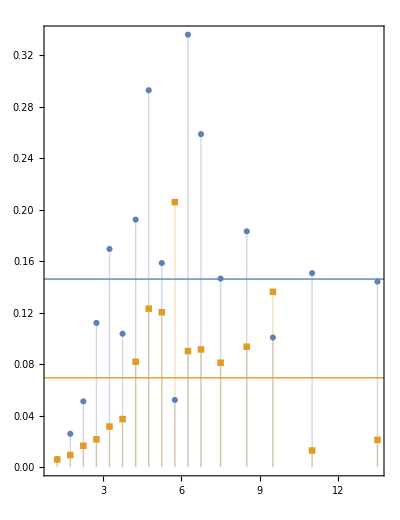

```mathematica
pTmeanError=ListPlot[{
pTmeanRelativeError1,pTmeanRelativeError2
},PlotRange->All,Evaluate@style,AspectRatio->1.3,Filling->Bottom,FrameLabel->MaTeX/@{"p_T \\ [\\mathrm{GeV}]","\\text{relative error}"},PlotLegends->MaTeX/@{"N=10^5","N=10^6"},PlotMarkers->Automatic,
Prolog->{
{colors[[1]],InfiniteLine[{0,pTmeanRelativeError1Mean},{1,0}]},{colors[[2]],InfiniteLine[{0,pTmeanRelativeError2Mean},{1,0}]}
}]
```

#### Export

```mathematica
Export["Thesis/Graphics/pT_mean_error.pdf",pTmeanError]
```

Thesis/Graphics/pT_mean_error.pdf

#### Data

```mathematica
pp5ErrorData=f@@@Import["Pythia/Data/pT cross section/Error Analysis/pT5.csv"];
pp6ErrorData=f@@@Import["Pythia/Data/pT cross section/Error Analysis/pT6.csv"];
```

```mathematica
pp5Error=Transpose[{pp5ErrorData[[All,1]],RelativeError/@pp5ErrorData[[All,2]]}];
pp6Error=Transpose[{pp6ErrorData[[All,1]],RelativeError/@pp6ErrorData[[All,2]]}];
```

```mathematica
pp5ErrorMean=Mean[pp5Error[[All,2]]]
```

193359.

## Azimuthal correlations

### Statistical error

#### Data

```mathematica
pp6hard1=Import["Pythia/Tests/Error Analysis/pp6_hard_1.csv"];
pp6hard2=Import["Pythia/Tests/Error Analysis/pp6_hard_2.csv"];
pp6hard3=Import["Pythia/Tests/Error Analysis/pp6_hard_3.csv"];
pp6hard4=Import["Pythia/Tests/Error Analysis/pp6_hard_4.csv"];
```

```mathematica
pp6soft1=Import["Pythia/Tests/Error Analysis/pp6_soft_1.csv"];
pp6soft2=Import["Pythia/Tests/Error Analysis/pp6_soft_2.csv"];
pp6soft3=Import["Pythia/Tests/Error Analysis/pp6_soft_3.csv"];
pp6soft4=Import["Pythia/Tests/Error Analysis/pp6_soft_4.csv"];
```

```mathematica
azimuthMean61=HistogramMean[{pp6hard1,pp6hard2,pp6hard3,pp6hard4}];
azimuthMean62=HistogramMean[{pp6soft1,pp6soft2,pp6soft3,pp6soft4}];
azimuthMeanRelativeError61=Map[RelativeError,azimuthMean61,{2}];
azimuthMeanRelativeError62=Map[RelativeError,azimuthMean62,{2}];
azimuthMeanRelativeError61Mean=Mean[azimuthMeanRelativeError61[[All,2]]];
azimuthMeanRelativeError62Mean=Mean[azimuthMeanRelativeError62[[All,2]]];
```

```mathematica
pp7hard1=Import["Pythia/Tests/Error Analysis/pp7_hard_1.csv"];
pp7hard2=Import["Pythia/Tests/Error Analysis/pp7_hard_2.csv"];
pp7hard3=Import["Pythia/Tests/Error Analysis/pp7_hard_3.csv"];
pp7hard4=Import["Pythia/Tests/Error Analysis/pp7_hard_4.csv"];
```

```mathematica
pp7soft1=Import["Pythia/Tests/Error Analysis/pp7_soft_1.csv"];
pp7soft2=Import["Pythia/Tests/Error Analysis/pp7_soft_2.csv"];
pp7soft3=Import["Pythia/Tests/Error Analysis/pp7_soft_3.csv"];
pp7soft4=Import["Pythia/Tests/Error Analysis/pp7_soft_4.csv"];
```

```mathematica
azimuthMean71=HistogramMean[{pp7hard1,pp7hard2,pp7hard3,pp7hard4}];
azimuthMean72=HistogramMean[{pp7soft1,pp7soft2,pp7soft3,pp7soft4}];
azimuthMeanRelativeError71=Map[RelativeError,azimuthMean71,{2}];
azimuthMeanRelativeError72=Map[RelativeError,azimuthMean72,{2}];
azimuthMeanRelativeError71Mean=Mean[azimuthMeanRelativeError71[[All,2]]];
azimuthMeanRelativeError72Mean=Mean[azimuthMeanRelativeError72[[All,2]]];
```

#### Relative error N = 10^6

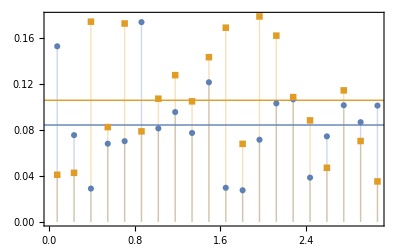

```mathematica
azimuthMeanError1=ListPlot[{
azimuthMeanRelativeError61,azimuthMeanRelativeError62
},PlotRange->All,Evaluate@style,Filling->Bottom,PlotLegends->MaTeX/@{"\\text{HardQCD}","\\text{SoftQCD (non-diffractive)}"},PlotMarkers->Automatic,PlotLabel->MaTeX["N=10^6"],
Prolog->{
{colors[[1]],InfiniteLine[{0,azimuthMeanRelativeError61Mean},{1,0}]},{colors[[2]],InfiniteLine[{0,azimuthMeanRelativeError62Mean},{1,0}]}
}]
```

#### Relative error N = 10^7

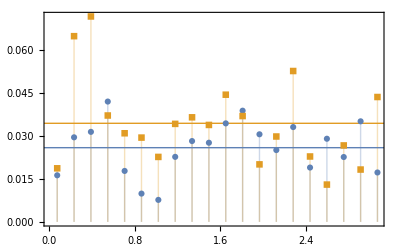

```mathematica
azimuthMeanError2=ListPlot[{
azimuthMeanRelativeError71,azimuthMeanRelativeError72
},PlotRange->All,Evaluate@style,Filling->Bottom,PlotMarkers->Automatic,PlotLabel->MaTeX["N=10^7"],
Prolog->{
{colors[[1]],InfiniteLine[{0,azimuthMeanRelativeError71Mean},{1,0}]},{colors[[2]],InfiniteLine[{0,azimuthMeanRelativeError72Mean},{1,0}]}
}]
```

#### Grid

```mathematica
azimuthMeanError=PlotGrid[
{{azimuthMeanError1},
{azimuthMeanError2}},
FrameLabel->MaTeX/@{"\\Delta\\phi","\\text{relative error}"},
Spacings->{None,50}
]
```

-Graphics-

#### Export

```mathematica
Export["Thesis/Graphics/azimuth_mean_error.pdf",azimuthMeanError]
```

Thesis/Graphics/azimuth_mean_error.pdf

### Histogram error (old)

#### Data

```mathematica
pp6HardErrorData=f@@@Import["Pythia/Data/Error Analysis/Experimental/pp6_hard.csv"];
pp6SoftErrorData=f@@@Import["Pythia/Data/Error Analysis/Experimental/pp6_soft.csv"];
```

```mathematica
pp7HardErrorData=f@@@Import["Pythia/Data/Error Analysis/Experimental/pp7_hard.csv"];
pp7SoftErrorData=f@@@Import["Pythia/Data/Error Analysis/Experimental/pp7_soft.csv"];
```

```mathematica
pp6HardError=Transpose[{pp6HardErrorData[[All,1]],#["Uncertainty"]&/@pp6HardErrorData[[All,2]]}];
pp6SoftError=Transpose[{pp6SoftErrorData[[All,1]],#["Uncertainty"]&/@pp6SoftErrorData[[All,2]]}];
```

```mathematica
pp7HardError=Transpose[{pp7HardErrorData[[All,1]],#["Uncertainty"]&/@pp7HardErrorData[[All,2]]}];
pp7SoftError=Transpose[{pp7SoftErrorData[[All,1]],#["Uncertainty"]&/@pp7SoftErrorData[[All,2]]}];
```

```mathematica
pp6HardErrorMean=Mean[pp6HardError[[All,2]]];
pp6SoftErrorMean=Mean[pp6SoftError[[All,2]]];
```

```mathematica
pp7HardErrorMean=Mean[pp7HardError[[All,2]]];
pp7SoftErrorMean=Mean[pp7SoftError[[All,2]]];
```

#### Relative error

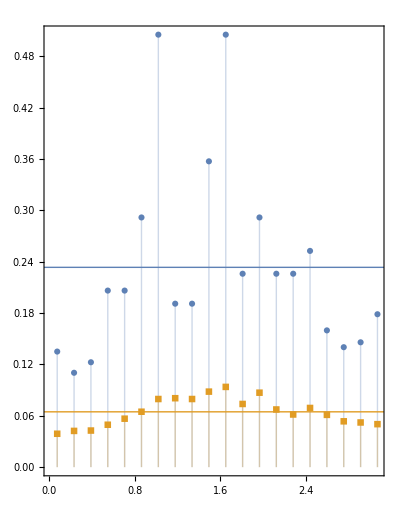

```mathematica
ListPlot[{
pp6HardError,pp7HardError
},PlotRange->All,Evaluate@style,AspectRatio->1.3,Filling->Bottom,FrameLabel->MaTeX/@{"p_T \\ [\\mathrm{GeV}]","\\text{relative error}"},PlotLegends->MaTeX/@{"N=10^6","N=10^7"},PlotMarkers->Automatic,
Prolog->{
{colors[[1]],InfiniteLine[{0,pp6HardErrorMean},{1,0}]},{colors[[2]],InfiniteLine[{0,pp7HardErrorMean},{1,0}]}
}]
```

### Histogram error

#### Data (increase count)

```mathematica
pp6NoMPIHard15=Import/@FileNames["*.csv","Pythia/Data/pp/delta_phi/No MPI/Hard15/1e6"];
pp6NoMPISoft=Import/@FileNames["*.csv","Pythia/Data/pp/delta_phi/No MPI/Soft/1e6"];
```

```mathematica
pp7NoMPIHard15=Import/@FileNames["*.csv","Pythia/Data/pp/delta_phi/No MPI/Hard15/1e7"];
pp7NoMPISoft=Import/@FileNames["*.csv","Pythia/Data/pp/delta_phi/No MPI/Soft/1e7"];
```

```mathematica
pp9NoMPIHard15=Import/@FileNames["*.csv","Pythia/Data/pp/delta_phi/No MPI/Hard15/1e9"];
pp9NoMPISoft=Import/@FileNames["*.csv","Pythia/Data/pp/delta_phi/No MPI/Soft/1e9"];
```

#### Relative error

```mathematica
errorAnalysisPlot1=PlotGrid[{
MapIndexed[
ListPlot[(h@@@#)&/@#1,
Evaluate@style,
Joined->True,
IntervalMarkers->"Bands",
PlotStyle->{Automatic,Dashed,DotDashed},
PlotLegends->Conditional[
Placed[
MaTeX/@{"\\text{HardQCD}","\\text{SoftQCD (non-diffractive)}"},
Above],
First[#2]==Length[#1]],
PlotRange->{All,{0.1,0.7}},
PlotLabel->Conditional[
MaTeX["N=10^6"],
First[#2]==1]
]&,Transpose[{pp6NoMPIHard15[[1;;4]],pp6NoMPISoft[[1;;4]]}]
],
MapIndexed[
ListPlot[(h@@@#)&/@#1,
Evaluate@style,
Joined->True,
IntervalMarkers->"Bands",
PlotStyle->{Automatic,Dashed,DotDashed},
PlotRange->{All,{0.1,0.7}},
PlotLabel->Conditional[
MaTeX["N=10^7"],
First[#2]==1]
]&,Transpose[{pp7NoMPIHard15[[1;;4]],pp7NoMPISoft[[1;;4]]}]
]
}ᵀ,ImageSize->400,
FrameLabel->MaTeX/@{"\\Delta\\phi","\\mathrm{d}\\sigma/\\mathrm{d}\\Delta\\phi"},
Spacings->{{None,50},None},
PlotLabels->(Placed[#,{Center,0.9}]&/@(MaTeX/@{
"1.4<(p_T)_2<2.0",
"1.4<(p_T)_2<2.0",
"2.0<(p_T)_2<2.4",
"2.0<(p_T)_2<2.4",
"2.4<(p_T)_2<2.8",
"2.4<(p_T)_2<2.8",
"2.8<(p_T)_2<5.0",
"2.8<(p_T)_2<5.0"}))
]
```

-Graphics-

```mathematica
errorAnalysisPlot2=PlotGrid[{
MapIndexed[
ListPlot[(Transpose[{#[[All,1]],#[[All,3]]}])&/@#1,
Evaluate@style,
Filling->Bottom,
PlotMarkers->Automatic,
PlotLegends->Conditional[
Placed[
MaTeX/@{"\\text{HardQCD}","\\text{SoftQCD (non-diffractive)}"},
Above],
First[#2]==Length[#1]],
PlotRange->{All,Automatic},
PlotLabel->Conditional[
MaTeX["N=10^6"],
First[#2]==1]
]&,Transpose[{pp6NoMPIHard15[[1;;4]],pp6NoMPISoft[[1;;4]]}]
],
MapIndexed[
ListPlot[(Transpose[{#[[All,1]],#[[All,3]]}])&/@#1,
Evaluate@style,
Filling->Bottom,
PlotMarkers->Automatic,
PlotRange->{All,Automatic},
PlotLabel->Conditional[
MaTeX["N=10^7"],
First[#2]==1]
]&,Transpose[{pp7NoMPIHard15[[1;;4]],pp7NoMPISoft[[1;;4]]}]
]
}ᵀ,ImageSize->400,
FrameLabel->MaTeX/@{"\\Delta\\phi","\\text{relative error}"},
PlotLabels->(Placed[#,{Center,0.9}]&/@(MaTeX/@{
"1.4<(p_T)_2<2.0",
"1.4<(p_T)_2<2.0",
"2.0<(p_T)_2<2.4",
"2.0<(p_T)_2<2.4",
"2.4<(p_T)_2<2.8",
"2.4<(p_T)_2<2.8",
"2.8<(p_T)_2<5.0",
"2.8<(p_T)_2<5.0"}))
]
```

-Graphics-

#### Export

```mathematica
Export["Thesis/Graphics/error_analysis_1.pdf",errorAnalysisPlot1]
Export["Thesis/Graphics/error_analysis_2.pdf",errorAnalysisPlot2]
```

Thesis/Graphics/error_analysis_1.pdf

Thesis/Graphics/error_analysis_2.pdf

### DPS vs MPI

#### Data

```mathematica
pp7DPS10Hard15=Import/@FileNames["*_dps10.csv","Pythia/Data/pp/delta_phi/DPS/Hard15/1e7"];
pp7DPS25Hard15=Import/@FileNames["*_dps25.csv","Pythia/Data/pp/delta_phi/DPS/Hard15/1e7"];
pp7DPSHard15=HistogramIntervalize/@Transpose[{pp7DPS10Hard15,pp7DPS25Hard15}];
```

```mathematica
pp7DPS10Soft=Import/@FileNames["*_dps10.csv","Pythia/Data/pp/delta_phi/DPS/Soft/1e7"];
pp7DPS25Soft=Import/@FileNames["*_dps25.csv","Pythia/Data/pp/delta_phi/DPS/Soft/1e7"];
pp7DPSSoft=HistogramIntervalize/@Transpose[{pp7DPS10Soft,pp7DPS25Soft}];
```

```mathematica
pp7MPIHard15=Import/@FileNames["*.csv","Pythia/Data/pp/delta_phi/MPI/Hard15/1e7"];
pp7MPISoft=Import/@FileNames["*.csv","Pythia/Data/pp/delta_phi/MPI/Soft/1e7"];
```

```mathematica
pp9DPS10Hard15=Import/@FileNames["*_dps10.csv","Pythia/Data/pp/delta_phi/DPS/Hard15/1e9"];
pp9DPS25Hard15=Import/@FileNames["*_dps25.csv","Pythia/Data/pp/delta_phi/DPS/Hard15/1e9"];
pp9DPSHard15=HistogramIntervalize/@Transpose[{pp9DPS10Hard15,pp9DPS25Hard15}];
```

```mathematica
pp9DPS10Soft=Import/@FileNames["*_dps10.csv","Pythia/Data/pp/delta_phi/DPS/Soft/1e9"];
pp9DPS25Soft=Import/@FileNames["*_dps25.csv","Pythia/Data/pp/delta_phi/DPS/Soft/1e9"];
pp9DPSSoft=HistogramIntervalize/@Transpose[{pp9DPS10Soft,pp9DPS25Soft}];
```

```mathematica
pp9MPIHard15=Import/@FileNames["*.csv","Pythia/Data/pp/delta_phi/MPI/Hard15/1e9"];
pp9MPISoft=Import/@FileNames["*.csv","Pythia/Data/pp/delta_phi/MPI/Soft/1e9"];
```

#### Comparison

```mathematica
DPSMPIComparison=PlotGrid[{
MapIndexed[
ListPlot[#1,
Evaluate@style,
Joined->True,
IntervalMarkers->"Bands",
PlotStyle->{Automatic,Dashed},
PlotLegends->Conditional[
MaTeX/@{"\\text{DPS}","\\text{MPI}","\\text{No MPI}"},
First[#2]==Length[#1]],
PlotRange->{All,{0,1}},
PlotLabel->Conditional[
MaTeX["\\text{HardQCD} \\ (\\hat{p}_T^{\\text{min}}=1.5)"],
First[#2]==1]
]&,Transpose[{pp9DPSHard15[[1;;4]],(h@@@#)&/@pp9MPIHard15[[1;;4]](*,(h@@@#)&/@pp9NoMPIHard15[[1;;4]]*)}]
],
MapIndexed[
ListPlot[#1,
Evaluate@style,
Joined->True,
IntervalMarkers->"Bands",
PlotStyle->{Automatic,Dashed},
PlotRange->{All,{0,1}},
PlotLabel->Conditional[
MaTeX["\\text{SoftQCD (non-diffractive)}"],
First[#2]==1]
]&,Transpose[{pp9DPSSoft[[1;;4]],(h@@@#)&/@pp9MPISoft[[1;;4]](*,(h@@@#)&/@pp9NoMPISoft[[1;;4]]*)}]
]
}ᵀ,ImageSize->400,
FrameLabel->MaTeX/@{"\\Delta\\phi","\\mathrm{d}\\sigma/\\mathrm{d}\\Delta\\phi"},
PlotLabels->(Placed[#,{Center,0.9}]&/@(MaTeX/@{
"1.4<(p_T)_2<2.0",
"1.4<(p_T)_2<2.0",
"2.0<(p_T)_2<2.4",
"2.0<(p_T)_2<2.4",
"2.4<(p_T)_2<2.8",
"2.4<(p_T)_2<2.8",
"2.8<(p_T)_2<5.0",
"2.8<(p_T)_2<5.0"}))
]
```

-Graphics-

#### Export

```mathematica
Export["Thesis/Graphics/dps_mpi_comparison.pdf",DPSMPIComparison]
```

Thesis/Graphics/dps_mpi_comparison.pdf

### HardQCD vs SoftQCD

#### Data (increase count)

```mathematica
pp7NoMPIHard10=Import/@FileNames["*.csv","Pythia/Data/pp/delta_phi/No MPI/Hard10/1e7"];
pp7NoMPIHard20=Import/@FileNames["*.csv","Pythia/Data/pp/delta_phi/No MPI/Hard20/1e7"];
```

#### Comparison

```mathematica
hardSoftPlot=PlotGrid[{
MapIndexed[
ListPlot[h@@@#&/@#1,
Evaluate@style,
Joined->True,
IntervalMarkers->"Bands",
PlotStyle->{Automatic,Dashed,DotDashed,Dotted},
PlotLegends->Conditional[
Placed[
MaTeX/@{
"\\text{HardQCD} \\ (\\hat{p}_T^{\\text{min}}=1.0)",
"\\text{HardQCD} \\ (\\hat{p}_T^{\\text{min}}=1.5)",
"\\text{HardQCD} \\ (\\hat{p}_T^{\\text{min}}=2.0)",
"\\text{SoftQCD (non-diffractive)}"},
Above],
First[#2]==2],
PlotRange->{All,{0,1}}
]&,Transpose[{pp7NoMPIHard10[[1;;2]],pp7NoMPIHard15[[1;;2]],pp7NoMPIHard20[[1;;2]],pp7NoMPISoft[[1;;2]]}]
],
MapIndexed[
ListPlot[h@@@#&/@#1,
Evaluate@style,
Joined->True,
IntervalMarkers->"Bands",
PlotStyle->{Automatic,Dashed,DotDashed,Dotted},
PlotRange->{All,{0,1}}
]&,Transpose[{pp7NoMPIHard10[[3;;4]],pp7NoMPIHard15[[3;;4]],pp7NoMPIHard20[[3;;4]],pp7NoMPISoft[[3;;4]]}]
]
}ᵀ,ImageSize->450,
FrameLabel->MaTeX/@{"\\Delta\\phi","\\mathrm{d}\\sigma/\\mathrm{d}\\Delta\\phi"},
PlotLabels->(Placed[#,{Center,0.9}]&/@(MaTeX/@{
"1.4<(p_T)_2<2.0",
"2.0<(p_T)_2<2.4",
"2.4<(p_T)_2<2.8",
"2.8<(p_T)_2<5.0"}))
]
```

-Graphics-

#### Export

```mathematica
Export["Thesis/Graphics/hard_soft_comparison.pdf",hardSoftPlot]
```

Thesis/Graphics/hard_soft_comparison.pdf

### Nuclear modifications

#### Data (increase count)

```mathematica
pp8DPS10Hard15=Import/@FileNames["*_dps10.csv","Pythia/Data/pp/delta_phi/DPS/Hard15/1e8"];
pp8DPS25Hard15=Import/@FileNames["*_dps25.csv","Pythia/Data/pp/delta_phi/DPS/Hard15/1e8"];
pp8DPSHard15=HistogramIntervalize/@Transpose[{pp8DPS10Hard15,pp8DPS25Hard15}];
```

```mathematica
pp8DPS10Soft=Import/@FileNames["*_dps10.csv","Pythia/Data/pp/delta_phi/DPS/Soft/1e8"];
pp8DPS25Soft=Import/@FileNames["*_dps25.csv","Pythia/Data/pp/delta_phi/DPS/Soft/1e8"];
pp8DPSSoft=HistogramIntervalize/@Transpose[{pp8DPS10Soft,pp8DPS25Soft}];
```

```mathematica
Al8DPS10Hard15=Import/@FileNames["*_dps10.csv","Pythia/Data/pAl/delta_phi/DPS/Hard15/1e8"];
Al8DPS25Hard15=Import/@FileNames["*_dps25.csv","Pythia/Data/pAl/delta_phi/DPS/Hard15/1e8"];
Al8DPSHard15=HistogramIntervalize/@Transpose[{Al8DPS10Hard15,Al8DPS25Hard15}];
```

```mathematica
Al8DPS10Hard15nPDF=Import/@FileNames["*_dps10.csv","Pythia/Data/pAl/delta_phi/DPS/Hard15 nPDF/1e8"];
Al8DPS25Hard15nPDF=Import/@FileNames["*_dps25.csv","Pythia/Data/pAl/delta_phi/DPS/Hard15 nPDF/1e8"];
Al8DPSHard15nPDF=HistogramIntervalize/@Transpose[{Al8DPS10Hard15nPDF,Al8DPS25Hard15nPDF}];
```

```mathematica
Al8DPS10Soft=Import/@FileNames["*_dps10.csv","Pythia/Data/pAl/delta_phi/DPS/Soft/1e8"];
Al8DPS25Soft=Import/@FileNames["*_dps25.csv","Pythia/Data/pAl/delta_phi/DPS/Soft/1e8"];
Al8DPSSoft=HistogramIntervalize/@Transpose[{Al8DPS10Soft,Al8DPS25Soft}];
```

```mathematica
Au8DPS10Hard15=Import/@FileNames["*_dps10.csv","Pythia/Data/pAu/delta_phi/DPS/Hard15/1e8"];
Au8DPS25Hard15=Import/@FileNames["*_dps25.csv","Pythia/Data/pAu/delta_phi/DPS/Hard15/1e8"];
Au8DPSHard15=HistogramIntervalize/@Transpose[{Au8DPS10Hard15,Au8DPS25Hard15}];
```

```mathematica
Au8DPS10Hard15nPDF=Import/@FileNames["*_dps10.csv","Pythia/Data/pAu/delta_phi/DPS/Hard15 nPDF/1e8"];
Au8DPS25Hard15nPDF=Import/@FileNames["*_dps25.csv","Pythia/Data/pAu/delta_phi/DPS/Hard15 nPDF/1e8"];
Au8DPSHard15nPDF=HistogramIntervalize/@Transpose[{Au8DPS10Hard15nPDF,Au8DPS25Hard15nPDF}];
```

```mathematica
Au8DPS10Soft=Import/@FileNames["*_dps10.csv","Pythia/Data/pAu/delta_phi/DPS/Soft/1e8"];
Au8DPS25Soft=Import/@FileNames["*_dps25.csv","Pythia/Data/pAu/delta_phi/DPS/Soft/1e8"];
Au8DPSSoft=HistogramIntervalize/@Transpose[{Au8DPS10Soft,Au8DPS25Soft}];
```

#### Comparison

```mathematica
nuclearModificationComparison=PlotGrid[{
MapIndexed[
ListPlot[#1,
Evaluate@style,
Joined->True,
IntervalMarkers->"Bands",
PlotStyle->{Automatic,Dashed,DotDashed},
PlotLegends->Conditional[
Placed[
MaTeX/@{"p+p","p+\\text{Al}","p+\\text{Au}"},
Above],
First[#2]==Length[#1]],
PlotRange->{All,{0.1,0.7}},
PlotLabel->Conditional[
MaTeX["\\text{HardQCD}"],
First[#2]==1]
]&,Transpose[{pp8DPSHard15[[1;;4]],Al8DPSHard15[[1;;4]],Au8DPSHard15[[1;;4]]}]
],
MapIndexed[
ListPlot[#1,
Evaluate@style,
Joined->True,
IntervalMarkers->"Bands",
PlotStyle->{Automatic,Dashed},
PlotRange->{All,{0.1,0.7}},
PlotLabel->Conditional[
MaTeX["\\text{HardQCD (nPDF)}"],
First[#2]==1]
]&,Transpose[{pp8DPSHard15[[1;;4]],Al8DPSHard15nPDF[[1;;4]],Au8DPSHard15nPDF[[1;;4]]}]
],
MapIndexed[
ListPlot[#1,
Evaluate@style,
Joined->True,
IntervalMarkers->"Bands",
PlotStyle->{Automatic,Dashed},
PlotRange->{All,{0.1,0.7}},
PlotLabel->Conditional[
MaTeX["\\text{SoftQCD (non-diffractive)}"],
First[#2]==1]
]&,Transpose[{pp8DPSSoft[[1;;4]],Al8DPSSoft[[1;;4]],Au8DPSSoft[[1;;4]]}]
]
}ᵀ,ImageSize->500,
FrameLabel->MaTeX/@{"\\Delta\\phi","\\mathrm{d}\\sigma/\\mathrm{d}\\Delta\\phi"},
PlotLabels->(Placed[#,{Center,0.9}]&/@(MaTeX/@{
"1.4<(p_T)_2<2.0",
"1.4<(p_T)_2<2.0",
"1.4<(p_T)_2<2.0",
"2.0<(p_T)_2<2.4",
"2.0<(p_T)_2<2.4",
"2.0<(p_T)_2<2.4",
"2.4<(p_T)_2<2.8",
"2.4<(p_T)_2<2.8",
"2.4<(p_T)_2<2.8",
"2.8<(p_T)_2<5.0",
"2.8<(p_T)_2<5.0",
"2.8<(p_T)_2<5.0"}))
]
```

-Graphics-

#### Export

```mathematica
Export["Thesis/Graphics/nuclear_mod_comparison.pdf",nuclearModificationComparison]
```

Thesis/Graphics/nuclear_mod_comparison.pdf

### Nuclear suppression

#### Data

```mathematica
pp10DPS10Soft=Import/@FileNames["*_dps10.csv","Pythia/Data/pp/delta_phi/DPS/Soft/1e10"];
pp10DPS25Soft=Import/@FileNames["*_dps25.csv","Pythia/Data/pp/delta_phi/DPS/Soft/1e10"];
pp10DPSSoft=HistogramIntervalize/@Transpose[{pp10DPS10Soft,pp10DPS25Soft}];
```

```mathematica
Al10DPS10Soft=Import/@FileNames["*_dps10.csv","Pythia/Data/pAl/delta_phi/DPS/Soft/1e10"];
Al10DPS25Soft=Import/@FileNames["*_dps25.csv","Pythia/Data/pAl/delta_phi/DPS/Soft/1e10"];
Al10DPSSoft=HistogramIntervalize/@Transpose[{Al10DPS10Soft,Al10DPS25Soft}];
```

```mathematica
Au10DPS10Soft=Import/@FileNames["*_dps10.csv","Pythia/Data/pAu/delta_phi/DPS/Soft/1e10"];
Au10DPS25Soft=Import/@FileNames["*_dps25.csv","Pythia/Data/pAu/delta_phi/DPS/Soft/1e10"];
Au10DPSSoft=HistogramIntervalize/@Transpose[{Au10DPS10Soft,Au10DPS25Soft}];
```

#### Comparison

```mathematica
nuclearSuppression=PlotGrid[{
MapIndexed[
ListPlot[#1,
Evaluate@style,
Joined->True,
IntervalMarkers->"Bands",
PlotStyle->{Automatic,Dashed,DotDashed},
PlotLegends->Conditional[
MaTeX/@{"p+p","p+\\text{Al}","p+\\text{Au}"},
First[#2]==Length[#1]],
PlotRange->{All,{0.1,0.7}}
]&,Transpose[{pp10DPSSoft[[1;;4]],Al10DPSSoft[[1;;4]],Au10DPSSoft[[1;;4]]}]
]
}ᵀ,ImageSize->500,
FrameLabel->MaTeX/@{"\\Delta\\phi","\\mathrm{d}\\sigma/\\mathrm{d}\\Delta\\phi"},
PlotLabels->(Placed[#,{Center,0.9}]&/@(MaTeX/@{
"1.4<(p_T)_2<2.0",
"2.0<(p_T)_2<2.4",
"2.4<(p_T)_2<2.8",
"2.8<(p_T)_2<5.0"}))
]
```

-Graphics-

#### Export

```mathematica
Export["Thesis/Graphics/nuclear_mod_comparison.pdf",nuclearModificationComparison]
```

Thesis/Graphics/nuclear_mod_comparison.pdf